Preprint/Working Draft

This document is a preprint and working draft intended for community feedback.
It has not been peer-reviewed and has not been formally published.

© 2026 - Donald Airey. All rights reserved.

This work is intended for submission to a peer-reviewed journal.
Public posting of this draft does not constitute prior publication and does not waive the author’s right to publish a revised version.

# Gravity and Action from the Evolution of a Complex Manifold

## A Kinematic Origin for Gravity, Action, and Cosmic Evolution

## Abstract

We present a bilocal geometric framework in which separations are defined between ordered pairs of events rather than by a local infinitesimal metric. This construction is motivated by the need to represent global evolution in a manner that remains well-defined over finite separations while admitting a smooth local limit. The resulting geometry is formulated on a complex manifold with an imaginary temporal coordinate and a real spatial coordinate. A constant manifold acceleration sets the global spatial scale and produces a parabolic cycle of expansion and contraction. In the local reduction, the same acceleration scale yields a circular-orbit envelope consistent with the baryonic Tully-Fisher relation. At cosmological scales, the resulting analytic distance--redshift relation predicts the Pantheon+ Type~Ia supernova luminosity distances on the SH0ES-calibrated absolute scale and yields a lower covariance-weighted  than Planck-calibrated FLRW, without invoking dark matter or dark energy. The parabolic metric evolution, when combined with standard recombination microphysics, yields an acoustic angular scale consistent with Planck measurements.

-Graphics-

Figure 1. Schematic representation of the complex parabolic metric manifold. Latitude lines correspond to spatial slices at fixed epoch, while longitude lines trace the temporal evolution of the manifold.

## Setup and Definitions

### Environment Cleanup

```mathematica
Quiet@ClearAll["Global`*"];
```

### Typesetting Rules

```mathematica
MakeBoxes[accelerationSI,StandardForm]:=InterpretationBox[StyleBox["𝒜",FontFamily->"Times"],accelerationSI];
MakeBoxes[angularScale, StandardForm] := InterpretationBox[SubscriptBox["θ", "*"],angularScale]; 
MakeBoxes[baryonDensity,StandardForm]:=InterpretationBox[SubscriptBox["ρ","b"],baryonDensity];
MakeBoxes[boltzmannConstant,StandardForm]:=InterpretationBox[SubscriptBox["k",StyleBox["B",FontSlant->"Plain"]],boltzmannConstant];MakeBoxes[causalityHorizon,StandardForm]:=InterpretationBox[SubscriptBox["d","ch"],causalityHorizon];
MakeBoxes[centrifugalAcceleration,StandardForm]:=InterpretationBox[SubscriptBox["a","cent"],centrifugalAcceleration];
MakeBoxes[cephidDistanceModuli,StandardForm]:=InterpretationBox[SubscriptBox["μ","cep"],cephidDistanceModuli];
MakeBoxes[cephidRedshifts,StandardForm]:=InterpretationBox[SubscriptBox["z","cep"],cephidRedshifts];
MakeBoxes[chiSquared,StandardForm]:=InterpretationBox[SuperscriptBox["χ","2"],chiSquared];
MakeBoxes[covarianceMatrix,StandardForm]:=InterpretationBox[StyleBox["Σ",Bold],covarianceMatrix];
MakeBoxes[curvatureDensity,StandardForm]:=InterpretationBox[SubscriptBox["Ω","k"],curvatureDensity];
MakeBoxes[electronDensity,StandardForm]:=InterpretationBox[SubscriptBox["n","e"],electronDensity];
MakeBoxes[emissionTime,StandardForm]:=InterpretationBox[SubscriptBox["t","e"],emissionTime];
MakeBoxes[flrwComovingDistance,StandardForm]:=InterpretationBox[SubscriptBox["D","C,FLRW"],flrwComovingDistance];
MakeBoxes[flrwDistanceModuli,StandardForm]:=InterpretationBox[SubscriptBox["μ","FLRW"],flrwDistanceModuli];
MakeBoxes[flrwLuminousDistance,StandardForm]:=InterpretationBox[SubscriptBox["D","L,FLRW"],flrwLuminousDistance];
MakeBoxes[freeElectronFraction,StandardForm]:=InterpretationBox[SubscriptBox["X","e"],freeElectronFraction];
MakeBoxes[gasMass,StandardForm]:=InterpretationBox[SubscriptBox["M","g"],gasMass];
MakeBoxes[gasMassError,StandardForm]:=InterpretationBox[SubscriptBox["σ",SubscriptBox["M","g"]],gasMassError];
MakeBoxes[hubbleConstant,StandardForm]:=InterpretationBox[SubscriptBox["H","0"],hubbleConstant];
MakeBoxes[hydrogenMass,StandardForm]:=InterpretationBox[SubscriptBox["M","h"],hydrogenMass];
MakeBoxes[initialVelocity,StandardForm]:=InterpretationBox[SubscriptBox["V","0"],initialVelocity];
MakeBoxes[initialVelocitySI,StandardForm]:=InterpretationBox[SubscriptBox[StyleBox["𝒱",FontFamily->"Times"],"0"],initialVelocitySI];
MakeBoxes[inwardAcceleration,StandardForm]:=InterpretationBox[SubscriptBox["a","in"],inwardAcceleration];
MakeBoxes[lambdaDensity,StandardForm]:=InterpretationBox[SubscriptBox["Ω","λ"],lambdaDensity];
MakeBoxes[localSignalSpeed,StandardForm]:=InterpretationBox[SubscriptBox["c","loc"],localSignalSpeed];MakeBoxes[logTime,StandardForm]:=InterpretationBox[SubscriptBox["t","log"],logTime];
MakeBoxes[massDensity,StandardForm]:=InterpretationBox[SubscriptBox["Ω","m"],massDensity];
MakeBoxes[maximumMass,StandardForm]:=InterpretationBox[SubscriptBox["M","max"],maximumMass];
MakeBoxes[maximumRadius,StandardForm]:=InterpretationBox[SubscriptBox["r","max"],maximumRadius];
MakeBoxes[meanPhotonEnergy,StandardForm]:=InterpretationBox[RowBox[{"⟨",SubscriptBox["E","γ"],"⟩"}],meanPhotonEnergy];MakeBoxes[modelMassLog,StandardForm]:=InterpretationBox[SubscriptBox[OverscriptBox["M","^"],"log"],modelMassLog];
MakeBoxes[observationTime,StandardForm]:=InterpretationBox[SubscriptBox["t","o"],observationTime];
MakeBoxes[observationTimeSI,StandardForm]:=InterpretationBox[SubscriptBox[StyleBox["𝓉",FontFamily->"Times"],"o"],observationTimeSI];
MakeBoxes[observedMass,StandardForm]:=InterpretationBox[SubscriptBox["M","obs"],observedMass];
MakeBoxes[observedMassError,StandardForm]:=InterpretationBox[SubscriptBox["σ","M"],observedMassError];
MakeBoxes[observedMassLog,StandardForm]:=InterpretationBox[SubscriptBox["M","log"],observedMassLog];
MakeBoxes[observedMassLogError,StandardForm]:=InterpretationBox[SubscriptBox["σ","M,log"],observedMassLogError];
MakeBoxes[observedVelocity,StandardForm]:=InterpretationBox[SubscriptBox["v","obs"],observedVelocity];
MakeBoxes[observedVelocityError,StandardForm]:=InterpretationBox[SubscriptBox["σ","v"],observedVelocityError];
MakeBoxes[observedVelocityLogError,StandardForm]:=InterpretationBox[SubscriptBox["σ","v,log"],observedVelocityLogError];
MakeBoxes[particleHorizon,StandardForm]:=InterpretationBox[SubscriptBox["d","p"],particleHorizon];
MakeBoxes[photonDensity,StandardForm]:=InterpretationBox[SubscriptBox["ρ","γ"],photonDensity];
MakeBoxes[photonEnergyDensity,StandardForm]:=InterpretationBox[SubscriptBox["u","γ"],photonEnergyDensity];
MakeBoxes[photonNumberDensity,StandardForm]:=InterpretationBox[SubscriptBox["n","γ"],photonNumberDensity];
MakeBoxes[photonTemperature,StandardForm]:=InterpretationBox[SubscriptBox["T","γ"],photonTemperature];MakeBoxes[pmeComovingDistance,StandardForm]:=InterpretationBox[SubscriptBox["D","C"],pmeComovingDistance];
MakeBoxes[pmeLuminousDistance,StandardForm]:=InterpretationBox[SubscriptBox["D","L"],pmeLuminousDistance];
MakeBoxes[pmePrediction,StandardForm]:=InterpretationBox[SubscriptBox["μ","pme"],pmePrediction];
MakeBoxes[redshiftFromTime,StandardForm]:=InterpretationBox[SubscriptBox["z","t"],redshiftFromTime];
MakeBoxes[redshiftIterator,StandardForm]:=InterpretationBox[SuperscriptBox["z","′"],redshiftIterator];
MakeBoxes[redshiftOfRecombination,StandardForm]:=InterpretationBox[SubscriptBox["z","*"],redshiftOfRecombination];
MakeBoxes[reducedPlanckConstant,StandardForm]:=InterpretationBox[StyleBox["ℏ",FontSlant->"Italic"],reducedPlanckConstant];MakeBoxes[residuals,StandardForm]:=InterpretationBox[OverscriptBox["r","→"],residuals];
MakeBoxes[scaleFactorFromTime,StandardForm]:=InterpretationBox[SubscriptBox["a","t"],scaleFactorFromTime];
MakeBoxes[soundHorizon,StandardForm]:=InterpretationBox[SubscriptBox["r","s"],soundHorizon];
MakeBoxes[speedOfCausality,StandardForm]:=InterpretationBox[SubscriptBox["c","c"],speedOfCausality];
MakeBoxes[speedOfSound,StandardForm]:=InterpretationBox[SubscriptBox["c","s"],speedOfSound];
MakeBoxes[stellarMass,StandardForm]:=InterpretationBox[SubscriptBox["M","⋆"],stellarMass];
MakeBoxes[stellarMassError,StandardForm]:=InterpretationBox[SubscriptBox["σ",SubscriptBox["M","*"]],stellarMassError];
MakeBoxes[supernovaDistanceModuli,StandardForm]:=InterpretationBox[SubscriptBox["μ","sne"],supernovaDistanceModuli];
MakeBoxes[supernovaRedshifts,StandardForm]:=InterpretationBox[SubscriptBox["z","sne"],supernovaRedshifts];
MakeBoxes[thomsonOpticalDepth,StandardForm]:=InterpretationBox[SubscriptBox["τ","T"],thomsonOpticalDepth];
MakeBoxes[thomsonScatteringCrossSection,StandardForm]:=InterpretationBox[SubscriptBox["σ","T"],thomsonScatteringCrossSection];
MakeBoxes[thomsonScatteringRate,StandardForm]:=InterpretationBox[SubscriptBox["Γ","T"],thomsonScatteringRate];
MakeBoxes[timeFromRedshift,StandardForm]:=InterpretationBox[SubscriptBox["t","z"],timeFromRedshift];
MakeBoxes[timeIterator,StandardForm]:=InterpretationBox[SuperscriptBox["t","′"],timeIterator];
MakeBoxes[timeOfRecombination,StandardForm]:=InterpretationBox[SubscriptBox["t","*"],timeOfRecombination];
MakeBoxes[transverseCircumference, StandardForm] := InterpretationBox[SubscriptBox["C", "⊥"],transverseCircumference]; 
MakeBoxes[transverseRadius, StandardForm] := InterpretationBox[SubscriptBox["R", "⊥"],transverseRadius]; 
MakeBoxes[Δs0,StandardForm]:=InterpretationBox[SuperscriptBox["Δs","0"],Δs0];
MakeBoxes[Δs1,StandardForm]:=InterpretationBox[SuperscriptBox["Δs","1"],Δs1];
MakeBoxes[Δs2,StandardForm]:=InterpretationBox[SuperscriptBox["Δs","2"],Δs2];
MakeBoxes[Δxe1,StandardForm]:=InterpretationBox[SubsuperscriptBox["Δx","e","1"],Δxe1];
MakeBoxes[Δxo1,StandardForm]:=InterpretationBox[SubsuperscriptBox["Δx","o","1"],Δxo1];
```

## Introduction

Cosmological observations tightly constrain theoretical descriptions of the universe. Measurements of the cosmic microwave background (CMB) fix early-universe conditions and global geometry with high precision [1], while Type Ia supernovae (SNe Ia) probe the late-time expansion history through the luminosity distance-redshift relation [2]. Although each dataset is internally consistent, discrepancies arise when parameters inferred from early- and late-time observations are compared. In particular, the tension in the Hubble constant [1, 3] indicates that the standard cosmological model may be incomplete.

Historically, such discrepancies have been addressed by extending the model. The cosmological constant was introduced to permit a static universe [4] and abandoned following the discovery of expansion [5]. Galaxy rotation curves motivated the introduction of non-baryonic dark matter [6], and supernova evidence for accelerated expansion led to the reintroduction of the cosmological constant as dark energy [7, 8]. While these additions yield a phenomenologically successful framework, the dominant components of the cosmic energy budget remain physically unexplained [1]. More recent approaches introduce additional degrees of freedom, including time-varying dark energy [9], further increasing the parametric structure of the model.

We develop a kinematic framework in which large-scale evolution and local gravitational phenomena arise from a common geometric structure, termed the Parabolic Metric Evolution (PME). Local metric descriptions specify infinitesimal separations, so finite separations between distant events must be constructed by integrating along a chosen connection; in a globally evolving system, this construction can depend on both the path and the evolution of the geometry. The PME framework replaces this path-dependent procedure with a bilocal definition that assigns separations directly to ordered event pairs while admitting a consistent local limit. Motion on the manifold is governed by a single intrinsic kinematic scale, eliminating the need for multiple independent cosmological parameters and linking global expansion and local dynamics to a common geometric origin. The geometric structure of the manifold is illustrated in Fig. 1.

This approach differs from relativistic metric gravity in its bilocal definition of separation and from modified-gravity models [10, 11] in that the characteristic acceleration scale is not introduced phenomenologically but inherited from the global manifold kinematics by the local-reduction regime. Cosmological evolution, gravity, and the laws governing motion are thereby unified through a single acceleration scale determined by the manifold kinematics.

The resulting construction defines a minimal kinematic closure: the lowest-order geometric structure that consistently relates finite separations, global evolution, and local dynamics within a single framework, without introducing independent dynamical components. The bilocal definition of separation provides a representation of finite intervals compatible with global evolution, and the restriction to a single intrinsic acceleration scale selects the simplest nontrivial homogeneous dynamics beyond uniform motion, yielding a closed and self-consistent description across cosmological and local regimes.

## Bilocal Geometry

### Foundational Structure

The framework is defined by the following postulates:

Physical separations are defined bilocally between ordered pairs of events.

The manifold evolution is governed by a constant acceleration scale .

The manifold is parameterized by an intrinsic evolution coordinate .

Observable time is defined operationally through null exchange, providing an invariant ordering of events. The intrinsic evolution parameter is related to this observable time by the projection , which fixes the real-imaginary decomposition of temporal and spatial functionals and serves as a defining structural postulate of the framework.

All subsequent results follow from this structure.

### Bilocal Spatial Separation

Let  denote an emission event and  an observation event, with the bilocal interval constructed from a temporal functional obtained from accumulated evolution between slices and a spatial functional defined from separations on the emission and observation slices.

-Graphics-

Figure 2. Geometric construction of the bilocal interval between emission event  and observation event , showing the accumulated temporal evolution and the symmetric midpoint spatial separation between scaled slices.

The bilocal construction is illustrated in Figure 2. The spatial slices scale with a global manifold extent , so the separations at emission and observation satisfy

Δx_e^1/L[t_e]==Δx_o^1/L[t_o]

```mathematica
comovingRelation=Subscript[Δx, e]^1/L[Subscript[t, e]]==Subscript[Δx, o]^1/L[Subscript[t, o]];
```

Imposing symmetry under interchange of emission and observation together with a smooth coincidence limit motivates adopting the midpoint average as the minimal symmetric choice,

,

,

```mathematica
Δs^1=Simplify[Expand[Subscript[Δx, o]^1-1/2 (Subscript[Δx, o]^1-Subscript[Δx, e]^1)]]
```

1/2 (Δx_e^1+Δx_o^1)

### Invariance of the Bilocal Interval

Consider a bilocal scalar constructed from the temporal and spatial endpoint functionals . We adopt a quadratic form as the lowest-order scalar consistent with finite separations, ensuring that the local reduction yields a well-defined null condition while avoiding higher-order dependence on endpoint structure,

.

Under interchange of the ordered endpoints , the temporal functional changes sign while the symmetric spatial functional does not, so the mixed term changes sign. Invariance therefore requires .

In the local reduction, sufficiently small endpoint separations render the temporal and spatial functionals linear in the coordinate increments. The null condition must define a finite null ratio, which requires both temporal and spatial contributions to enter non-degenerately so that the null condition defines a finite null ratio. The interval therefore reduces to

.

The remaining quadratic form is therefore constrained up to a positive overall factor and a relative scaling between the temporal and spatial functionals. These functionals are not arbitrary coordinates but are identified with the canonical imaginary and real components of the complex manifold, with this identification fixing their relative normalization. The bilocal interval is therefore

,

```mathematica
Δs^2=(Δs^0)^2+(Δs^1)^2;
```

with  purely imaginary and  real.

### Imaginary Velocity

The intrinsic evolution of the manifold is parameterized by a coordinate . Observable time is introduced by the projection , so that , fixing the real-imaginary decomposition used in the bilocal construction.

```mathematica
χ[t_]=ⅈ t;
```

With constant intrinsic acceleration ,the velocity scale along the manifold history follows from integration with respect to ,

.

Substituting  gives , which evaluates to

,

```mathematica
v[t_]=Simplify[∫A D[χ[t], t]ⅆt-ⅈ Subscript[V, 0]]
```

ⅈ (-V_0+A t)

where  is an integration constant representing the initial expansion rate of the manifold.

### Induced Spatial Evolution

The observable spatial extent arises from integrating the imaginary velocity along the imaginary temporal direction. The global spatial scale of the manifold is therefore . Substituting the expression for  and using  gives . Evaluating the integral yields

.

```mathematica
L[t_]=∫v[t] D[χ[t], t]ⅆt
```

V_0 t-(A t^2)/2

### Manifold Deceleration

The intrinsic evolution is defined along , while observable dynamics are expressed in the projected time coordinate  with . Rewriting the manifold extent in terms of  yields its observable form. Differentiating twice with respect to  gives

,

```mathematica
D[L[t], {t,2}]
```

-A

so the manifold extent evolves with a constant kinematic deceleration of magnitude , which is universal and independent of position or epoch.

## Cosmological Distance

Observable cosmological distances follow from the bilocal interval defined in equation (5).

### Temporal Separation

The temporal component of the bilocal interval is obtained from the accumulated tangent evolution along the manifold history between the emission and observation parameters  and , . Substituting Eq. (6) gives

.

Evaluating the integral yields

.

```mathematica
Δs^0=Simplify[∫_Subscript[t, e]^Subscript[t, o] v[t]ⅆt]
```

-1/2 ⅈ (t_e-t_o) (-2 V_0+A (t_e+t_o))

The temporal separation is purely imaginary and depends only on the endpoints.

### Spatial Separation

Solving equation (1) for the emission separation gives

.

```mathematica
Subscript[Δx, e]^1=First[Subscript[Δx, e]^1/.Solve[comovingRelation,Subscript[Δx, e]^1]]
```

((A (t_e)^2-2 t_e V_0) Δx_o^1)/(t_o (-2 V_0+A t_o))

Because spatial slices scale with the manifold extent  and the slice separations satisfy the bilocal scaling relation given in equation (3), the spatial component becomes

.

```mathematica
Δs^1
```

1/2 (Δx_o^1+((A (t_e)^2-2 t_e V_0) Δx_o^1)/(t_o (-2 V_0+A t_o)))

### Bilocal Metric Formula

Substituting the temporal and spatial separations into equation (5) yields the interval relating the emission and observation events,

+

```mathematica
Δs^2
```

-1/4 (t_e-t_o)^2 (-2 V_0+A (t_e+t_o))^2+1/4 (Δx_o^1+((A (t_e)^2-2 t_e V_0) Δx_o^1)/(t_o (-2 V_0+A t_o)))^2

### Redshift Relation

Redshift is defined observationally by the ratio of observed to emitted wavelength,

.

We identify wavelength with a comoving spatial separation and assume that such separations scale with the manifold extent, so that .

.

Using equation (7), the emission epoch  is expressed in terms of  and the observed redshift ,

,

```mathematica
Subscript[t, z][z_]=Simplify[First[Subscript[t, e]/.Solve[z==(L[Subscript[t, o]]-L[Subscript[t, e]])/L[Subscript[t, e]],Subscript[t, e]]]]
```

(V_0+V_0 z-√((1+z) ((V_0)^2-2 A V_0 t_o+A^2 (t_o)^2+(V_0)^2 z)))/(A+A z)

where the negative branch is chosen so that .

Substituting into equation (13) and imposing the null condition  yields the observable spatial separation,

.

```mathematica
Subscript[Δx, o]^1=Subscript[Δx, o]^1/.Simplify[Solve[Δs^2==0,Subscript[Δx, o]^1]]⟦2⟧;
```

```mathematica
Subscript[D, C][z_]=Simplify[Subscript[Δx, o]^1/.Subscript[t, e]->Subscript[t, z][z],{z>0,Subscript[t, o] (A Subscript[t, o]-2 Subscript[V, 0])<0}]
```

(t_o (2 V_0-A t_o) z)/(2+z)

### Causal Structure

The null structure of the bilocal interval also determines the extent of causal connectivity on the manifold. The largest spatial separation permitted by null ordering is obtained from equation (13) with the emission event at the origin of the manifold history, , and the observation event at epoch . Solving the null condition  for the observed separation gives the causal horizon

.

```mathematica
Subscript[d, ch][t_]=FullSimplify[Subscript[Δx, o]^1/.{Subscript[t, e]->0,Subscript[t, o]->t}]
```

t (2 V_0-A t)

Differentiating the causal horizon gives the expansion rate of the causal boundary,

.

This quantity defines the rate at which the accessible causal domain can be extended under the operational clock, and therefore characterizes the growth of the causally orderable region.

Comparing the causal horizon with the manifold extent  defined in equation (7) yields

.

```mathematica
Simplify[(Subscript[d, ch][t])/L[t]]
```

2

The causal horizon is therefore twice the manifold extent at all epochs, placing the entire last-scattering surface within a single causal region. Because the homogeneous manifold acceleration introduces no preferred direction, the large-scale isotropy of the cosmic microwave background follows directly from the geometry.

## Gravity

When the temporal interval between neighboring events is small compared with the characteristic evolution scale of the manifold extent , the bilocal construction admits a smooth local reduction yielding an effective acceleration field inherited from the manifold kinematics.

### Coincidence Limit

The local description is obtained as the coincidence limit of the bilocal interval as the endpoint separation tends to zero. Let the observation event occur at epoch  and the emission event at , with . To extract the leading nontrivial local structure, the temporal and spatial bilocal functionals are expanded to first and second orders in .

Using the local expansion of the manifold extent,

,

the slice-separation relation gives

.

Hence

,

so the bilocal spatial component becomes

to leading order in . Over the same interval, the temporal component is

.

Substituting these leading terms into equation~(\ref{eq:bilocal_interval}) yields

.

which is the emergent local interval obtained from the coincidence limit of the bilocal geometry. The local interval therefore defines a tangent of fixed magnitude  shared by all trajectories at epoch , whose projections onto orthogonal temporal and spatial components give rise to timelike, null, and spacelike directions.

### Acceleration Field

Consider an event pair  whose temporal separation  satisfies . Expanding the manifold extent about a reference epoch  gives

.

Using equation (##), the quadratic term is governed by the constant local value . The local reduction therefore contains a homogeneous second-order contribution corresponding to a uniform deceleration of magnitude  inherited from the global manifold evolution, which provides the physical origin of gravity in the local limit. This uniform deceleration defines the background acceleration field underlying local gravitational dynamics.

The effective inward acceleration in a bound system decomposes into a homogeneous background and a sourced concentration,

.

```mathematica
Subscript[a, in][r_]=-A-(G M[r])/r^2
```

-A-(G M[r])/r^2

The background term  is uniform and has constant magnitude . In the absence of localized content, it defines the manifold evolution, and an inertial frame follows it without inducing concentration or depletion. Localized inertial content, however, resists this acceleration, redistributing the flux into spatial concentrations that define the sourced gravitational component  governing bound dynamics. The inertial parameter  entering this redistribution is the same quantity that weights the invariant separation in the construction of geometric action, so that the gravitational response corresponds to a redistribution of the inertia-weighted action-space separation underlying the local geometry.

### Minimal Local Closure

The bilocal construction fixes the homogeneous background acceleration scale  through the second-order local reduction of the manifold extent but does not determine the sourced concentration arising from spatial variations in inertial resistance. A weak-field closure is therefore required.

We adopt a minimal closure as the lowest-order local form consistent with locality, linearity in enclosed inertial content, rotational invariance, and additivity. These conditions restrict the sourced field to a divergence relation as the leading-order connection between field structure and inertial content, rather than an assumed inverse-square form. The concentration field therefore satisfies a divergence proportional to a local inertial density, with enclosed content given by its volume integral. In the weak-field limit, this density is dominated by rest mass and reduces to the baryonic density. All intrinsic kinematic scales are fixed by the acceleration scale , while the constant  sets the coupling to localized inertial content without introducing an additional kinematic scale.

For a spherically symmetric configuration the sourced acceleration is radial,

.

In the local-reduction regime relevant for gravitationally bound systems, the concentration field resides in three spatial dimensions, so spherical symmetry is defined with respect to ordinary 2-spheres in . The flux through a sphere of radius  is

Imposing flux conservation together with linearity in the enclosed inertial content gives

,

where  is the enclosed inertial content within radius , obtained from the local density by

,

and  is the empirical coupling relating inertial content to concentration of the background acceleration. Spherical symmetry then yields

,

and Gauss’s theorem gives

,

which is the Poisson equation for the sourced weak-field limit. In the weak-field regime relevant for galactic dynamics, the inertial density is dominated by baryonic rest-mass contributions, so .

### Circular Orbits

For a body in a circular orbit of radius  with tangential speed , the required centripetal acceleration is

.

```mathematica
Subscript[a, cent][r_]=-v^2/r;
```

Equating this with the inward acceleration from equation (27) gives

.

```mathematica
circularOrbitCondition=Subscript[a, cent][r]==Subscript[a, in][r]
```

-v^2/r==-A-(G M[r])/r^2

and multiplying by - gives

.

Then, solving for the enclosed baryonic mass gives

.

```mathematica
M[v_,r_]=M[r]/.Simplify[First@Solve[circularOrbitCondition,M[r]]]
```

(r (-A r+v^2))/G

### Circular-Orbit Solutions

Equation (37) defines the PME fundamental plane, a two-parameter family of circular-orbit solutions relating baryonic mass , orbital radius , and orbital speed .

For fixed orbital speed , the mass function  is a concave quadratic in . Differentiating gives

.

The mass therefore reaches a maximum at

.

```mathematica
Subscript[r, max][v_]=r/.First[Solve[D[M[v,r], r]==0,r]]
```

v^2/(2 A)

Substituting this radius into equation (37) yields the maximum baryonic mass compatible with a circular orbit at speed ,

.

```mathematica
Subscript[M, max][v_]=M[v,Subscript[r, max][v]]
```

v^4/(4 A G)

The surface  therefore defines a fundamental plane of circular-orbit solutions, as shown in Figure 3, with the ridge  giving the upper envelope of baryonic mass for a given orbital speed. Galaxies dominated by circular rotation are expected to saturate this boundary and follow a characteristic mass--velocity relation.

```mathematica
params={G->UnitConvert[Quantity["GravitationalConstant"],("Meters")^3/("Kilograms" ("Seconds")^2)],A->Quantity[1/10^11,("Meters")/("Seconds")^2]};
massSurface[v_,r_]:=ConditionalExpression[UnitConvert[M[v,r],"SolarMass"],QuantityMagnitude[UnitConvert[v^2-A r,("Meters")^2/("Seconds")^2]]>0]/.params;
massScale=1/Quantity[10^9,"SolarMass"];
fundamentalPlane=Plot3D[UnitConvert[massSurface[Quantity[v,("Kilometers")/("Seconds")],Quantity[r,"Kiloparsecs"]],"SolarMass"] massScale,{v,0,100},{r,0,30},AxesLabel->{Style["speed (km s^-1)",14],Style["radius (kpc)",14],Style["mass (10^9 M_☉)",14]},PlotRange->All,PlotStyle->Directive[GrayLevel[0.5]],MeshStyle->Directive[GrayLevel[0.3]],Lighting->"Neutral"];
maximumMassCurve=ParametricPlot3D[{v,QuantityMagnitude[UnitConvert[Subscript[r, max][Quantity[v,("Kilometers")/("Seconds")]],"Kiloparsecs"]],UnitConvert[Subscript[M, max][Quantity[v,("Kilometers")/("Seconds")]],"SolarMass"] massScale}/.params,{v,0,100},PlotStyle->{Directive[Red,Thick]},PlotPoints->100,MaxRecursion->4];
fundamentalPlaneFigure=Show[{fundamentalPlane,maximumMassCurve},ViewPoint->{-2,-3,1},ViewVertical->{0,0,1},ImageSize->Large]
```

-Graphics3D-

Figure 3. PME fundamental plane defined by equation (37). The baryonic mass surface  is shown as a function of orbital speed  and orbital radius  for an illustrative manifold acceleration scale . The red ridge marks the locus  corresponding to the maximum baryonic mass permitted by the manifold kinematics at each orbital speed. Galaxies populating this ridge reproduce the baryonic Tully-Fisher relation.

### Baryonic Tully-Fisher Relation

defines the scaling , consistent with the observed baryonic Tully--Fisher relation [12].

A characteristic acceleration scale in galaxy dynamics has previously been emphasized in frameworks such as MOND [10], in which the force law is modified to reproduce Tully-Fisher-type scaling.

The manifold acceleration  is determined empirically by fitting the circular-orbit envelope (equation (40)) to the SPARC galaxy sample of McGaugh, Lelli and Schombert [18], using the assumptions , , zero intrinsic mass-to-light uncertainty, and the quality cut . These rotationally supported disk systems are well suited to the analysis, as their kinematics closely follow the circular-orbit approximation.

For each galaxy the rotation curve provides an asymptotic circular velocity , while the baryonic mass  is computed as . The value of  is determined by minimizing the  statistic between the theoretical envelope and the observed  pairs.

The best-fit manifold acceleration is

.

```mathematica
tapURL="https://tapvizier.cds.unistra.fr/TAPVizieR/tap/sync";
adql="SELECT * FROM \"J/AJ/152/157/table1\"";
raw=Import[URLBuild[tapURL,<|"request"->"doQuery","lang"->"adql","format"->"csv","query"->adql|>],"CSV"];
header=First[raw];
rows=Rest[raw];
upsStar=0.5;
fracUpsErr=0.0;
gasFactor=1.33;
maxQual=3;
column=AssociationThread[header->Range[Length[header]]];
get[row_,key_]:=row[[column[key]]];
baryonicMass[row_]:=Module[{l36=N@get[row,"L3_6"],mhi=N@get[row,"MHI"]},upsStar*l36+gasFactor*mhi];
massError[row_]:=Module[{l36=N@get[row,"L3_6"],el36=N@get[row,"e_L3_6"],mhi=N@get[row,"MHI"],dist=N@get[row,"Dist"],edist=N@get[row,"e_Dist"],fracDist,eStarPhot,eStarML,eGasDist,eStarDist},fracDist=If[dist>0,edist/dist,0.0];
eStarPhot=upsStar*el36;
eStarML=fracUpsErr*upsStar*l36;
eStarDist=2*fracDist*(upsStar*l36);
eGasDist=2*fracDist*(gasFactor*mhi);
Sqrt[eStarPhot^2+eStarML^2+eStarDist^2+eGasDist^2]];
vflat[row_]:=N@get[row,"Vflat"];
vflatError[row_]:=N@get[row,"e_Vflat"];
validRowQ[row_]:=Module[{v=vflat[row],ev=vflatError[row],q=get[row,"Qual"]},NumericQ[v]&&NumericQ[ev]&&v>0&&ev>=0&&q<=maxQual];
goodRows=Select[rows,validRowQ];
btfrData=({baryonicMass[#],vflat[#],massError[#],vflatError[#]}&)/@goodRows;
```

```mathematica
G=UnitConvert[Quantity["GravitationalConstant"],("Meters")^3/("Kilograms" ("Seconds")^2)];
Msun=UnitConvert[Entity["Star","Sun"]["Mass"],"Kilograms"];
km=Quantity[1,"Kilometers"];
massScale=10.^9*Msun;
logBtfrData=Module[{mb,v,emb,ev},({mb,v,emb,ev}=#;
{Log10[mb],Log10[v],emb/(mb*Log[10]),ev/(v*Log[10])})&/@btfrData];
modelMass[Ak_?QuantityQ,v_?NumericQ]:=Module[{m},m=(Quantity[v,"Kilometers"/"Seconds"]^4)/(4 Ak G);
QuantityMagnitude[UnitConvert[m/(10.^9 Msun),1]]];
logModelMass[Ak_?QuantityQ,logv_?NumericQ]:=Log10[modelMass[Ak,10.^logv]];
chiSquareLog[Ak_?QuantityQ]:=Total[Module[{logmb,logv,slogmb,slogv,model,sigmaEff2},{logmb,logv,slogmb,slogv}=#;
model=logModelMass[Ak,logv];
sigmaEff2=slogmb^2+(4*slogv)^2;
(logmb-model)^2/sigmaEff2]&/@logBtfrData];
chiSquareLogFromLogA[aLog_?NumericQ]:=Module[{Ak},Ak=Quantity[10.^aLog,"Meters"/"Seconds"^2];
chiSquareLog[Ak]];
minimum=FindMinimum[chiSquareLogFromLogA[aLog],{aLog,Log10[3.*10^-11]},WorkingPrecision->30];
𝒜=Quantity[10.^(aLog/. minimum[[2]]),"Meters"/"Seconds"^2]
```

3.68788×10^-11 m/s^2

The observed galaxies follow the predicted  scaling across a wide range of baryonic masses and rotational velocities, as shown in Figure 4. The baryonic Tully-Fisher relation is a direct consequence of the constant-acceleration structure of the manifold and the power of four relation is the observational signature of the acceleration flux.

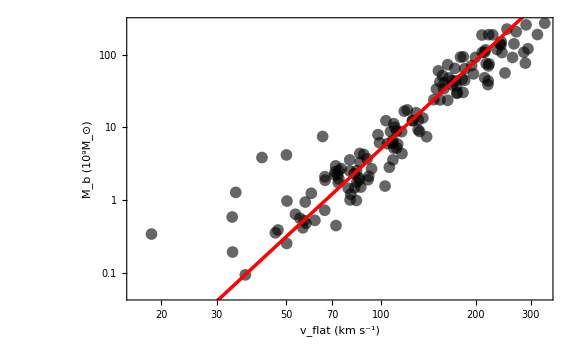

```mathematica
vMin=Min[btfrData⟦All,2⟧];
vMax=Max[btfrData⟦All,2⟧];
modelMass[v_]:=v^4/((4 A G) massScale)
observedPlot=ListLogLogPlot[btfrData⟦All,{2,1}⟧,Frame->True,Axes->False,FrameLabel->{Style[Row[{Subscript["v", "flat"]," (km s^-1)"}],14],Style[Row[{Subscript["M", "b"]," (",("10")^("9"),Subscript["M", "⊙"],")"}],14]},PlotStyle->{Directive[Black,Opacity[0.6]]},GridLines->Automatic,PlotMarkers->{Automatic,12},PlotRange->All];
modelPlot=LogLogPlot[modelMass[Quantity[v,("Kilometers")/("Seconds")]]/.A->𝒜,{v,vMin,vMax},PlotStyle->{Red,AbsoluteThickness[2.5]}];
btfrPlot=Show[observedPlot,modelPlot,ImageSize->Large]
```

Figure 4. Log-log plot of baryonic mass  versus outer rotation speed  for the SPARC galaxy sample of McGaugh, Lelli and Schombert [18]. Black circles show the observed galaxies. The solid red line shows the PME circular-orbit envelope evaluated at the best-fit acceleration.

### Global Acceleration Budget

The local closure fixes all non-homogeneous acceleration flux as sourced by inertial content. In the weak-field regime this reduces to baryonic mass. Integrating the flux law over the full homogeneous domain of scale  gives

.

Using the global relation between baryonic mass and the background acceleration scale,

,

yields

.

Thus the available concentration flux is fixed by the background scale  and is completely accounted for by baryonic mass. Local gravitational systems therefore correspond to partial redistributions of a finite acceleration budget, so gravitational collapse approaches a saturated configuration rather than an unbounded one.

Mach’s Bucket

The bilocal reduction introduces a homogeneous acceleration scale  fixed by the geometry of the manifold. This acceleration is not sourced by baryonic matter; instead, baryonic mass redistributes it through conservation of acceleration flux (equation (30)).

For a rotating system of radius  and tangential speed , circular motion requires an inward centripetal acceleration . In this framework, that requirement is met by redistributing the background field to produce the necessary inward concentration.

Because the total acceleration is finite, this redistribution cannot be local: any concentration within the system must be balanced globally. Rotational inertia therefore depends on the global distribution of mass through the shared acceleration field, providing a Machian interpretation.

### Regularity of the Manifold

Because the manifold acceleration scale is finite, collapse approaches saturated configurations of finite density and radius rather than singular limits. The manifold accordingly remains smooth under the evolution defined by the geometry and does not admit singular collapse.

Causal ordering is fixed by the intrinsic geometry of allowable separations, not by any imposed signal speed. Only trajectories consistent with this ordering admit an operational time parameter, excluding closed timelike curves and the associated causal paradoxes.

The causal structure and finite acceleration budget thereby avoid singularities and causal paradoxes.

## Local Dynamics

Having established the gravitational and causal structure, we now define the operational dynamics governing motion within the manifold.

### Operational Time

Imposing the null condition  on equation (25) gives

,

so that

.

This defines the null boundary of the local geometry and fixes the relation between spatial separation and temporal increment through the scale .

Observable time is defined operationally by null exchange between nearby worldlines. One tick of the clock is a complete round trip of a signal along null trajectories, and the temporal parameter  is identified with the number of such cycles, which defines an invariant ordering of events. The null relation ensures that each cycle corresponds to a fixed temporal increment set by the local scale  and restricts admissible trajectories to those consistent with this ordering.

The null relation therefore fixes the local causal structure and operational ordering of events. Observable motion and the invariant timelike interval both arise from this same local geometry, so causality, motion, and measurable duration are unified through the null structure of the manifold.

### Proper Time

Using the local interval defined in equation (25),

,

proper time defines the invariant timelike interval along admissible trajectories, , so that

,

giving

.

where .

### Local Momentum

A non-zero manifold acceleration defines a global acceleration flux that selects a timelike direction. The local interval arises from the Euclidean bilocal scalar (equation(5)) with orthogonal temporal (imaginary) and spatial (real) components, so it resolves as projections of a tangent of fixed magnitude whose spatial and temporal components vary with orientation. In the homogeneous local limit, this orientation is represented by an angle  relative to the flux.

Let  denote an increment of the underlying constant-magnitude tangent. Resolving the tangent via the local invariant (equation (25)), the orthogonal projections admit a representation in terms of an angle , yielding

.

Observable kinematics are defined with respect to the temporal parameter . In the homogeneous local limit, the measurable velocity may be expressed as

.

The null boundary is reached when , which requires  and therefore . Observable motion is accordingly restricted to the timelike domain . At this boundary, the underlying geometric structure remains well-defined through the orientation angle , but the kinematic description in terms of  ceases to apply. Beyond this limit, the projection geometry persists but no longer corresponds to observable motion; its continuation is defined in terms of phase evolution.

At this boundary, the underlying geometric structure remains well-defined through the orientation angle , but the kinematic description in terms of  ceases to apply. Beyond this limit, the projection geometry persists but no longer corresponds to observable motion and is instead associated with phase.

Momentum is defined from the observable velocity,

,

and is the spatial projection of the geometric momentum scale  with respect to the temporal parameter .

### Local Action

In the coincidence limit, the bilocal interval (equation~(\ref{eq:local_interval})) defines a local tangent of fixed magnitude and an invariant interval  describing local manifold separation. Weighting this invariant separation by the tangent momentum scale

,

defines the invariant geometric action increment,

,

with quadratic form

.

Using the local invariant

,

the action-space interval becomes

.

The temporal component defines the geometric energy scale associated with tangent evolution,

,

while the spatial component defines the corresponding geometric momentum scale, .

Evaluating the local interval on the tangent direction shows that the fixed-magnitude tangent satisfies , so that

,

and therefore

,

so that the invariant geometric action accumulates along the manifold tangent,

.

Observable action is obtained by projection into the timelike sector,

,

which defines the canonical momentum and observable Hamiltonian. The observable action therefore plays the role of the Hamilton-Jacobi principal function, while the invariant geometric action remains well-defined across the full manifold.

### Phase Evolution

The projection-based kinematic description applies within the timelike sector, where the local invariant defines a real proper-time interval. At the null boundary,  and , marking the limit of observable timelike motion. Beyond this boundary, observable motion ceases, while the invariant geometric structure remains well-defined and the geometric action continues to accumulate along the manifold tangent.

The continued evolution of this invariant scalar is represented as phase,

ϕ=S_geom/ℏ

where ℏ sets the scale relating geometric action to phase. Because action has units of length within the present framework, ℏ acquires the interpretation of a minimum indivisible bilocal separation, a necessary structural feature of a geometry that does not admit infinitesimal separations.

Phase evolution therefore represents the continuation of invariant geometric evolution beyond the proper-time-parametrized sector, while the underlying manifold evolution remains continuous across the null boundary.

## Late-Time Evolution

The distance-redshift relation derived from the bilocal interval predicts the late-time expansion history.

### Type Ia Supernova Sample

We use the Pantheon+ compilation of 1701 spectroscopically confirmed Type~Ia supernovae presented by Brout et~al. [2]. The publicly released Pantheon+SH0ES dataset provides the observed distance moduli , redshifts , and the full STAT+SYS covariance matrix for covariance-weighted  inference. The distance moduli are absolutely calibrated through the SH0ES determination of the Type Ia absolute magnitude .

### Luminosity Distance

The spatial separation predicted by the manifold geometry is given by equation (17). The luminosity distance follows from the standard relation . Substituting the spatial separation yields the corresponding analytic luminosity distance

.

```mathematica
Subscript[D, L][z_?NumberQ]=(1+z) Subscript[D, C][z]
```

(t_o (2 V_0-A t_o) z (1+z))/(2+z)

### Distance Modulus

Type Ia supernova observations are reported in terms of the distance modulus, which relates the observed luminosity distance to the measured brightness of each supernova,

.

```mathematica
Subscript[μ, pme][z_?NumberQ]=5 Log10[(Subscript[D, L][z])/(10 pc)];
```

### Manifold Kinematic Parameters

The local null scale at the observation epoch is

.

Operationally, photon exchange is used as a proxy for this local null scale, so the measured speed of light at the observation epoch determines , fixing the integration constant,

.

```mathematica
velocity=First[Subscript[V, 0]/.Solve[-ⅈ c==v[Subscript[t, o]],Subscript[V, 0]]]
```

c+A t_o

With the manifold acceleration  determined from the baryonic Tully-Fisher analysis, the Cepheid-calibrated Pantheon+ subset is used to determine the observation epoch  on the absolute distance scale. For each candidate value of , the corresponding  follows algebraically from equation (67), and theoretical distance moduli  are evaluated at the calibration-set redshifts. These are compared with the observed values , defining the residual vector

.

The best-fit observation epoch is obtained by minimizing the covariance-weighted chi-square statistic

,

where  is the full Pantheon+ STAT+SYS covariance matrix. The resulting best-fit value of  then determines , completing the kinematic parameter set. The resulting parameters are listed in Table 1.

```mathematica
pantheonDirectory="https://github.com/PantheonPlusSH0ES/DataRelease/raw/refs/heads/main/Pantheon+_Data/4_DISTANCES_AND_COVAR/";
dataUrl=StringJoin[pantheonDirectory,"Pantheon+SH0ES.dat"];
covarianceUrl=StringJoin[pantheonDirectory,"Pantheon+SH0ES_STAT+SYS.cov"];
pantheonData=Import[dataUrl,"Table",HeaderLines->1];
covarianceData=Import[covarianceUrl,"Table"];
rawCovariance=Flatten[covarianceData];
dimensionSize=rawCovariance[[1]];
covarianceMatrix=ArrayReshape[Rest[rawCovariance],{dimensionSize,dimensionSize}];
cephidMask=pantheonData[[All,14]];
cephidIndices=Flatten@Position[cephidMask,1];
supernovaIndices=Flatten@Position[cephidMask,0];
cephidData=pantheonData[[cephidIndices]];
cephidRedshifts=N@cephidData[[All,3]];
cephidDistanceModuli=N@cephidData[[All,13]];
cephidCovarianceMatrix=covarianceMatrix[[cephidIndices,cephidIndices]];
cephidCovarianceMatrix=N[(cephidCovarianceMatrix+Transpose[cephidCovarianceMatrix])/2];
supernovaData=pantheonData[[supernovaIndices]];
supernovaRedshifts=N@supernovaData[[All,3]];
supernovaDistanceModuli=N@supernovaData[[All,11]];
supernovaCovarianceMatrix=covarianceMatrix[[supernovaIndices,supernovaIndices]];
supernovaCovarianceMatrix=N[(supernovaCovarianceMatrix+Transpose[supernovaCovarianceMatrix])/2];
```

```mathematica
params={pc->QuantityMagnitude[UnitConvert[Quantity[1,"Parsecs"],"Meters"]],c->QuantityMagnitude[UnitConvert[Quantity["SpeedOfLight"],("Meters")/("Seconds")]],A->QuantityMagnitude[𝒜]};
χ^2[t_?NumericQ]:=Module[{r^(->)},r^(->)=Subscript[μ, cep]-Subscript[μ, pme]/@Subscript[z, cep]/.params/.{Subscript[t, o]->t,Subscript[V, 0]->(velocity/.params/.{Subscript[t, o]->t})};r^(->).LinearSolve[cephidCovarianceMatrix,r^(->)]]
result=FindMinimum[χ^2[Exp[Subscript[t, log]]],{Subscript[t, log],Log[10^17]},Method->"QuasiNewton",AccuracyGoal->6];
```

```mathematica
Subscript[𝓉, o]=Quantity[Exp[Subscript[t, log]/.result⟦2⟧],"Seconds"];
Subscript[𝒱, 0]=Quantity[velocity/.params/.{Subscript[t, o]->Exp[Subscript[t, log]/.result⟦2⟧]},("Meters")/("Seconds")];
initialConditions={A->𝒜,Subscript[V, 0]->Subscript[𝒱, 0],Subscript[t, o]->Subscript[𝓉, o]};
Grid[{{"A",ScientificForm[A,4]},{"V_0",ScientificForm[Subscript[V, 0],4]},{"t_o",ScientificForm[Subscript[t, o],4]}}/.initialConditions,Frame->All,ItemStyle->12]
```

A | 3.688×10^-11 m/s^2
V_0 | 3.164×10^8 m/s
t_o | 4.512×10^17 s

Table 1 - PME kinematic parameters determined from BTFR and Cepheid-calibrated Pantheon+ subset.

### Comparison with Observations

Figure 5 shows the PME prediction and the Planck 2018 FLRW model compared with the Pantheon+SH0ES data.

The Pantheon+SH0ES dataset provides observed distance moduli  calibrated on an absolute scale through the SH0ES determination of the Type~Ia supernova absolute magnitude. This calibration is applied identically to both models.

Each model predicts , which is mapped to  using the definition of  introduced earlier. We compare  to  using the full Pantheon+ STAT+SYS covariance matrix.

PME is evaluated using the fixed parameter set derived above. FLRW is evaluated using a spatially flat model specified by the Planck 2018 parameter set , , and  [1]. The comparison is performed on the out-of-sample supernovae, excluding the Cepheid calibration records.

The resulting covariance-weighted chi-square values are

,

for , corresponding to reduced values  and , respectively. PME predicts the observed distance moduli substantially more accurately than the Planck 2018 FLRW model across the Pantheon+SH0ES sample, without dark sector parameters.

```mathematica
pmeParams={A->𝒜,Subscript[V, 0]->Subscript[𝒱, 0],Subscript[t, o]->Subscript[𝓉, o],pc->UnitConvert[Quantity[1,"Parsecs"],"Meters"]};
flrwParams={Subscript[Ω, m]->0.315,Subscript[Ω, k]->0};
flrwParams=Join[flrwParams,{Subscript[Ω, λ]->(1-Subscript[Ω, m]-Subscript[Ω, k])/.flrwParams,Subscript[H, 0]->UnitConvert[Quantity[67.4,("Kilometers")/("Seconds" "Megaparsecs")]/. flrwParams,1/"Seconds"],pc->UnitConvert[Quantity[1,"Parsecs"],"Meters"],c->UnitConvert[Quantity["SpeedOfLight"],("Meters")/("Seconds")]}];
```

```mathematica
supernovaObservedPoints = Transpose[{supernovaRedshifts, supernovaDistanceModuli}]; 
pmePredictedPoints = Transpose[{supernovaRedshifts, pmePrediction /@ supernovaRedshifts /. pmeParams}]; 
observedPlot = ListPlot[supernovaObservedPoints, PlotStyle -> {Gray}, PlotMarkers -> {"●", Medium}, PlotRange -> All]; 
pmeLine = ListLinePlot[pmePredictedPoints, PlotStyle -> {Red, Thick}, PlotRange -> All]; 
hubbleFunction[z_] := Sqrt[massDensity*(1 + z)^3 + curvatureDensity*(1 + z)^2 + lambdaDensity];
hubbleFunctionSI[(z_)?NumericQ] := Evaluate[hubbleFunction[z] /. flrwParams];
flrwComovingDistance[z_] := (c/hubbleConstant)*NIntegrate[1/hubbleFunctionSI[redshiftIterator], {redshiftIterator, 0, z}]; 
flrwLuminousDistance[z_] := (1 + z)*flrwComovingDistance[z]; 
flrwDistanceModuli[(z_)?NumericQ] := 5*Log10[flrwLuminousDistance[z]/(10*pc)]; 
xMin = Min[supernovaRedshifts]; 
xMax = Max[supernovaRedshifts]; 
xRange = {xMin, xMax}; 
commonOptions = Sequence[ImageSize -> 700, PlotRangePadding -> Scaled[0.02], Frame -> True, FrameTicksStyle -> 12];
```

```mathematica
flrwPoints = Transpose[{supernovaRedshifts, flrwDistanceModuli /@ supernovaRedshifts /. flrwParams}]; 
flrwLine = ListLinePlot[flrwPoints, PlotStyle -> {RGBColor[0, 0, 1], Thick}, PlotRange -> All]; 
hubblePlot = Show[{observedPlot, pmeLine, flrwLine}, commonOptions, PlotRange -> {xRange, All}, FrameLabel -> {Style["Redshift (z)", 14], Style["Distance Modulus (μ)", 14]}, 
    FrameTicks -> {{Automatic, Automatic}, {Automatic, None}}, ImagePadding -> {{70, 20}, {0, 20}}];
```

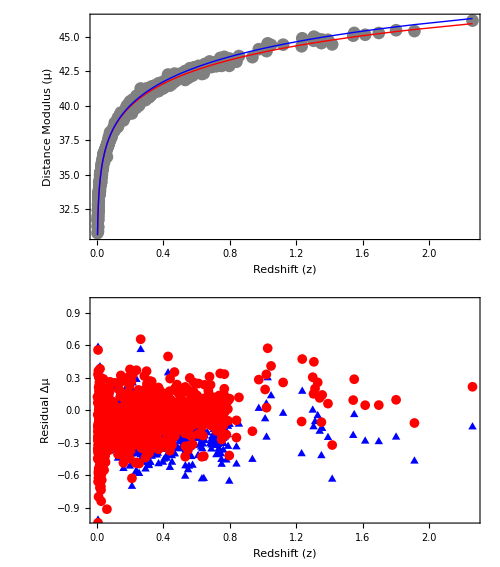

```mathematica
pmeResiduals = supernovaDistanceModuli - (pmePrediction /@ supernovaRedshifts /. pmeParams); 
flrwResiduals = supernovaDistanceModuli - (flrwDistanceModuli /@ supernovaRedshifts /. flrwParams); 
residualPlot = Show[ListPlot[{Transpose[{supernovaRedshifts, flrwResiduals}], Transpose[{supernovaRedshifts, pmeResiduals}]}, PlotStyle -> {Blue, Red}, 
     PlotMarkers -> {{"▲", Small}, {"●", Small}}], commonOptions, FrameLabel -> {Style["Redshift (z)", 14], Style["Residual Δμ", 14]}, 
    FrameTicks -> {{Automatic, Automatic}, {Automatic, None}}, ImagePadding -> {{70, 20}, {20, 0}}, PlotRange -> {{xMin, xMax}, {-1., 1.}}]; 
hubbleDiagram=GraphicsColumn[{hubblePlot, residualPlot}, Spacings -> 0, ImageSize -> 500]
```

Figure 5. Pantheon+SH0ES distance moduli with PME (red) and spatially flat FLRW (blue) predictions evaluated on the same absolute calibration. Lower panel shows residuals relative to each model.

```mathematica
chi2FromResiduals[res_]:=res.LinearSolve[supernovaCovarianceMatrix,res];
chi2PME=chi2FromResiduals[pmeResiduals];
chi2FLRW=chi2FromResiduals[flrwResiduals];
redChi2PME=chi2PME/Length[supernovaRedshifts];
redChi2FLRW=chi2FLRW/Length[supernovaRedshifts];
Grid[{{"Model","χ^2","χ_red^2"},{"PME",chi2PME,redChi2PME},{"FLRW",chi2FLRW,redChi2FLRW}},Frame->All,ItemStyle->12]
```

Model | χ^2 | χ_red^2
PME | 2726.5 | 1.67888
FLRW | 4049.24 | 2.49338

### Hubble Function

The Hubble expansion rate is defined by the fractional rate of change of the real spatial extent of the manifold, . Differentiating equation() gives , so

.

```mathematica
H[t_]=Simplify[v[t]/L[t]]
```

(2 ⅈ (V_0-A t))/(t (-2 V_0+A t))

Evaluating equation (##) at the observation epoch  using the best-fit manifold parameters gives the present-day expansion rate

H(t_o)=-66.5 km s^-1 Mpc^-1

```mathematica
UnitConvert[Im[H[Subscript[t, o]]/.initialConditions],("Kilometers")/("Seconds" "Megaparsecs")]
```

-66.5357 km/(Mpc s)

The Hubble constant therefore emerges as a prediction rather than a fitted parameter.

### Cosmic Time

The redshift–time relation differs from standard cosmological evolution due to the underlying parabolic evolution. Table II compares the resulting cosmic times with those from FLRW algorithms.

The parabolic expansion yields uniformly larger cosmic ages than FLRW, significantly extending the available time for early structure formation.

```mathematica
Grid[{{"z","PME(Myr)","FLRW(Myr)"},{0,14283,13791},{1,7039,5840},{10,1265,470},{100,137,16.4},{1000,13.9,0.429}},Frame->All,ItemStyle->12]
```

z | PME(Myr) | FLRW(Myr)
0 | 14283 | 13791
1 | 7039 | 5840
10 | 1265 | 470
100 | 137 | 16.4
1000 | 13.9 | 0.429

Table II - Cosmic time as a function of redshift. PME predictions are compared with FLRW values computed using Planck 2018 parameters.

## Early-Time Evolution

Independent constraints arise from the cosmic microwave background (CMB), whose acoustic scale probes the distance to last scattering relative to the sound horizon.

The expansion history is determined by the PME kinematics derived above, while recombination microphysics is evaluated using standard rate equations. Thermodynamic quantities are mapped using the scale factor

.

### Baryon and Photon Densities

The recombination history and pre-decoupling sound speed require the baryon and photon densities. The baryon density is fixed by the manifold acceleration scale rather than introduced as an independent cosmological parameter. This follows from the local divergence law (equation (33)), which relates the sourced acceleration field to the baryonic density.

For a homogeneous baryonic distribution of density  within a region of characteristic size , the enclosed mass is

,

```mathematica
M[L_]=(4π)/3 L^3 Subscript[ρ, b];
```

so the corresponding baryon-sourced acceleration at radius  is

.

Evaluating this expression at the present manifold extent , which contains the full homogeneous baryonic source, and identifying it with the inferred manifold acceleration  gives

,

hence

.

Using the kinematic parameters determined in the previous sections yields

.

```mathematica
gravitationalConstant=UnitConvert[Entity["PhysicalConstant","GravitationalConstant"]["Value"],"SIBase"];
Subscript[ρ, b]=Subscript[ρ, b]/.First[Solve[A==(M[L[Subscript[t, o]]] G)/L[Subscript[t, o]]^2/.initialConditions/.{G->gravitationalConstant},Subscript[ρ, b]]]
```

9.48781×10^-28 kg/m^3

This value is consistent with independent observational estimates of the present-day baryon density from primordial light-element abundances [13].

The photon density is determined from the measured CMB temperature . The mapping between temperature and photon density depends on the local geometric scale , so the photon density is treated as epoch dependent rather than a scaled constant. For a blackbody radiation field, the photon number density is

,

```mathematica
Subscript[k, B]=UnitConvert[Entity["PhysicalConstant","BoltzmannConstant"]["Value"],"SIBase"];
ℏ=UnitConvert[Entity["PhysicalConstant","ReducedPlanckConstant"]["Value"],"SIBase"];
Subscript[T, γ]=UnitConvert[Entity["PhysicalConstant","CosmicMicrowaveBackgroundTemperature"]["Value"],"SIBase"];
Subscript[n, γ][t_]:=(2 Zeta[3])/π^2((Subscript[k, B] Subscript[T, γ])/(ℏ (Subscript[V, 0]-A t)))^3;
```

and, following the geometric sign convention of Eq. (58), the mean photon energy is

.

```mathematica
⟨Subscript[E, γ]⟩=-(π^4 Subscript[k, B] Subscript[T, γ])/(30 Zeta[3]);
```

The corresponding photon energy density is

,

```mathematica
Subscript[u, γ][t_]:=Subscript[n, γ][t] ⟨Subscript[E, γ]⟩;
```

so the mass-equivalent photon density becomes

.

```mathematica
Subscript[ρ, γ][t_]:=-(Subscript[u, γ][t])/(Subscript[V, 0]-A t)^2
```

These densities determine the baryon-photon momentum ratio and the free-electron density entering the visibility function.

### Recombination Epoch

The recombination epoch is the time of maximum photon visibility, i.e. the most probable last-scattering time in the baryon-photon plasma.

To determine the ionization history, we evaluate the standard recombination rate equations using Recfast++ with the PME expansion geometry. The background evolution is provided by the PME Hubble function (equation (71)) in place of the FLRW algorithm, with the expansion rate governed by the best-fit manifold parameters. The baryon sector is specified by the present-day baryon density derived above. The resulting ionization history is used to interpolate the free-electron fraction  entering the visibility function. The free-electron number density  is defined as

,

```mathematica
pmeElectronFractionData=Import[CloudObject["https://www.wolframcloud.com/obj/5ee0ade7-823c-4871-8a8e-9717bf289d35"],"Table"];
{redshiftMin,redshiftMax}=MinMax[pmeElectronFractionData⟦All,1⟧];
Subscript[t, z][z_]=Subscript[t, e]/.Simplify[Solve[z==(L[Subscript[t, o]]-L[Subscript[t, e]])/L[Subscript[t, e]],Subscript[t, e]]]⟦1⟧;
Subscript[z, t][t_]=Simplify[L[Subscript[t, o]]/L[t]-1];
Subscript[a, t][t_]=Simplify[L[t]/L[Subscript[t, o]]];
Subscript[X, e]=Interpolation[pmeElectronFractionData⟦All,{1,2}⟧];
Subscript[M, h]=UnitConvert[Entity["Element","Hydrogen"]["AtomicMass"],"SIBase"];
Subscript[n, e][t_?QuantityQ]=Subscript[X, e][Subscript[z, t][t]] Subscript[ρ, b]/Subscript[M, h](1+Subscript[z, t][t])^3;
```

where  is the present-day baryon mass density,  is the proton mass.

The Thomson scattering rate is expressed in terms of the local particle density, cross section, and local geometric scale,

,

```mathematica
Subscript[σ, T]=UnitConvert[Entity["PhysicalConstant","ThomsonCrossSection"]["Value"],"SIBase"];
Subscript[Γ, T][t_?QuantityQ]:=Subscript[n, e][t] Subscript[σ, T] (Subscript[V, 0]-A t)
```

where  is the Thomson cross section. The optical depth is then defined as the accumulated interaction probability along the manifold history,

.

```mathematica
Subscript[τ, T][t_?QuantityQ]:=NIntegrate[Subscript[Γ, T][t']/.initialConditions,{t',t,Subscript[t, o]/.initialConditions},MaxRecursion->25]
```

The corresponding visibility function is

.

```mathematica
g[t_?QuantityQ]:=Subscript[Γ, T][t] Exp[-Subscript[τ, T][t]]
```

Evaluating  on the PME expansion background using the Recfast++ microphysics parametrization yields a maximum at ,  shown in Fig. 6.

```mathematica
numericVisibilityFunction[t_?NumericQ]:=QuantityMagnitude[g[Quantity[t,"Seconds"]]/.initialConditions];
tmin=QuantityMagnitude[Subscript[t, z][redshiftMax]/.initialConditions];
tmax=QuantityMagnitude[Subscript[t, z][redshiftMin]/.initialConditions];
SubStar[t]=Quantity[NArgMax[{numericVisibilityFunction[t],tmin<t<tmax},t,Method->"NelderMead",WorkingPrecision->15],"Seconds"];
SubStar[z]=Subscript[z, t][SubStar[t]]/.initialConditions
UnitConvert[SubStar[t],"Megayears"]
```

1038.61

13.4019 Myr

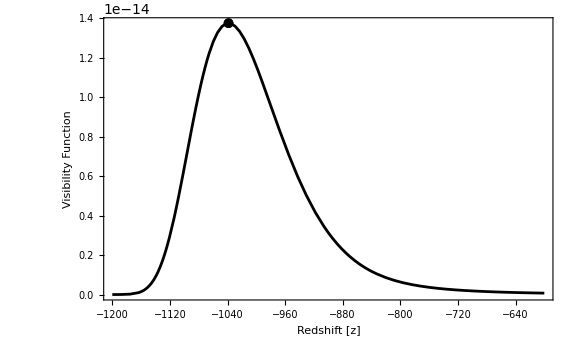

```mathematica
visibilityPlot=Plot[g[Subscript[t, z][z]/.initialConditions]/.initialConditions,{z,600,1200},ScalingFunctions->{"Reverse",Automatic},PlotStyle->{Black}, AxesOrigin->{1200,Automatic}];
maximumDepthMarkerPlot=ListPlot[{{SubStar[z],g[SubStar[t]]/.initialConditions}},ScalingFunctions->{"Reverse",Automatic},PlotStyle->{Black},PlotMarkers->{Automatic,Medium}];
visibilityFunction=Show[{visibilityPlot,maximumDepthMarkerPlot},Frame->True,FrameLabel->{Style["Redshift [z]",14], Style["Visibility Function",14]},ImageSize->Large]
```

Figure 6. Photon visibility function  evaluated using the recombination history on the PME expansion background. The peak defines the recombination epoch, yielding .

### Sound Horizon

Prior to recombination, baryons and photons form a tightly coupled fluid whose acoustic interaction distance defines the sound horizon. The thermodynamic evolution follows the scale factor  defined in equation (73).

The baryon–photon momentum ratio is defined as

,

```mathematica
R[t_?QuantityQ]:=(3 Subscript[ρ, b])/(4 Subscript[ρ, γ][t])Subscript[a, t][t]
```

giving the sound speed

.

```mathematica
Subscript[c, c][t_]:=(Subscript[d, ch])'[t]
```

```mathematica
Subscript[c, s][t_?QuantityQ]:=(Subscript[c, c][t])/(√(3 (1+R[t])))
```

The causal expansion rate  sets the rate at which interactions can be ordered through the operational clock and thus defines the effective causal scale entering the acoustic horizon integral, so that the sound horizon is

.

Evaluating this expression using the manifold parameters yields .

```mathematica
Subscript[r, s]=NIntegrate[Subscript[c, s][t']/.initialConditions,{t',0,SubStar[t]}];
UnitConvert[Subscript[r, s],"Megaparsecs"]
```

3.69092 Mpc

### Acoustic Angular Scale

The observed acoustic angle is determined by the ratio of the sound horizon at recombination to the bilocally assigned transverse size of the emission-observation pair.  denotes the circumference of the spatial slice at epoch , so the relevant transverse quantity is the effective bilocal transverse circumference associated with the ordered pair .

To define this quantity, consider a transverse bilocal path whose endpoints lie at antipodal points on the spatial slices at emission and observation. The transverse separations between antipodal points on those slices are therefore the corresponding slice circumferences,  and . Applying the bilocal spatial rule of equation (3) to this transverse configuration defines the bilocal spatial separation between antipodal transverse endpoints, which we identify as the effective transverse circumference,

.

Using the redshift relation from equation (15), this becomes

.

The corresponding effective transverse radius is

.

The acoustic angular scale is then

.

```mathematica
SubStar[θ]=Subscript[r, s]/(R_⊥);
```

Substituting the expression above for  gives

.

```mathematica
SubStar[θ]=SubStar[θ]/.R_⊥->(C_⊥)/(2 π);
```

Using equation (7) evaluated at  yields

.

```mathematica
SubStar[θ]=Simplify[SubStar[θ]/.(C_⊥->1/2 (L[Subscript[t, o]]+L[Subscript[r, s]])/.L[Subscript[r, s]]->L[Subscript[t, o]]/(1+SubStar[z]))];
```

Evaluating this expression with the manifold parameters gives

.

```mathematica
SubStar[θ]/.initialConditions
```

0.010284

Expressed in the conventional CMB notation,

100 θ_*=1.03

This result follows from the PME expansion geometry combined with standard recombination microphysics.

## Conclusion

A constrained bilocal construction on a complex manifold yields a quadratic interval whose local reduction yields a homogeneous acceleration scale. This single geometric scale governs both the parabolic evolution of the manifold and the redistribution of acceleration flux in gravitationally bound systems. The bilocal geometry produces an emergent local null constraint, defines an invariant action geometry, and admits a canonical decomposition into temporal and spatial contributions. From this structure, a Hamiltonian system and associated Hamilton--Jacobi equation arise as the projection of the inertia-weighted invariant geometric action into the timelike sector, so that particle motion follows geodesics of action space without introducing independent dynamical postulates, while phase evolution provides its continuation beyond the observable domain. Gravity and inertia therefore emerge as complementary manifestations of a conserved acceleration field inherited from the manifold kinematics.

The evolution implied by this construction yields a closed analytic distance-redshift relation, from which the Pantheon+ Type Ia supernova luminosity distances follow directly on an absolute scale. The same parameter set predicts the present-day Hubble constant and produces uniformly extended cosmic ages. In the local-reduction regime, redistribution of the homogeneous acceleration field generates an inverse-square sourced component and a circular-orbit envelope consistent with the observed baryonic Tully-Fisher relation. The acceleration scale inferred from galaxy dynamics then fixes the baryonic density of the homogeneous universe, linking galactic and cosmological observables without introducing non-baryonic dark matter or dark energy components.

The bilocal construction also determines the causal horizon and implies a constant ratio between the causal domain and manifold extent, placing the last-scattering surface within a single causal region and accounting for large-scale isotropy. The geometry yields a transverse scale for recombination that reproduces the observed acoustic angular scale. Because the available acceleration flux is finite, gravitational collapse approaches saturated configurations, eliminating curvature singularities and enforcing a globally ordered causal structure. Rotational inertia emerges from redistribution of the same finite acceleration budget, providing a Machian interpretation in which local inertial behavior depends on the global distribution of inertial content.

Evolution, causal structure, action, gravity, inertia, and dynamical law therefore arise from a common bilocal origin, with all dynamics derived from the momentum weighted invariant separation, providing a unified explanation of isotropy, galaxy rotation, Type~Ia supernova magnitudes, the acoustic scale, nonsingular gravitational collapse, the baryonic density, and the Hubble constant.

## References

[1] Planck Collaboration, N . Aghanim, et al. Planck 2018 results. vi. cosmological parameters. Astronomy & Astrophysics, 641: A6, 2020.

[2] Dillon Brout, Dan Scolnic, Boian Popovic, Adam G . Riess, et al. The Pantheon + analysis: Cosmological constraints from 1701 Type Ia supernovae. Astrophysical Journal, 938(2):110, 2022.

[3] Adam G.Riess, Wenlong Yuan, Lucas M.Macri, et al. A comprehensive measurement of the local value of the Hubble constant. Astrophysical Journal Letters, 934: L7, 2022.

[4] A.Einstein. Kosmologische betrachtungen zur allgemeinen relativit¨atstheorie. Sitzungsberichte der Koniglich Preußischen Akademie der Wissenschaften, pages 142–152, 1917.

[5] Edwin Hubble. A relation between distance and radial velocity among extra-galactic nebulae. Proceedings of the National Academy of Sciences,15(3):168–173,1929.

[6] Vera C.Rubin, W.Kent Ford, and Norbert Thonnard. Rotational properties of 21 SC galaxies with a large range of luminosities and radii. Astrophysical Journal,238:471–487,1980.

[7] Adam G . Riess, Alexei V . Filippenko, Peter Challis, et al. Observational evidence from supernovae for an accelerating universe and a cosmological constant. Astronomical Journal, 116 : 1009–1038, 1998.

[8] Saul Perlmutter, Greg Aldering, Gerson Goldhaber, et al. Measurements of Omega and Lambda from 42 high-redshift supernovae. Astrophysical Journal, 517 : 565–586, 1999.

[9] Eleonora Di Valentino, Alessandro Melchiorri, Joseph Silk, et al. In the realm of the Hubble tension—a review of solutions. Classical and Quantum Gravity, 38 (15) : 153001, 2021.

[10] Mordehai Milgrom. A modification of the Newtonian Dynamics as a possible alternative to the hidden mass hypothesis. Astrophysical Journal, 270 : 365–370, 1983.

[11] Stacy S . McGaugh, Federico Lelli, and James M . Schombert. Radial acceleration relation in rotationally supported galaxies. Physical Review Letters, 117 : 201101, 2016.

[12] Stacy S . McGaugh, James M . Schombert, Gregory D . Bothun, and W . J . G . de Blok . The baryonic tully–fisher relation . Astrophysical Journal Letters, 533 : L99–L102, 2000.

[13] R . J . Cooke, M . Pettini, K . M . Nollett, and R . Jorgenson . The primordial deuterium abun - dance of the most metal - poor damped lyman - α system . Astrophysical Journal, 830 : 148, 2016.